## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

Solutions to equations are returned as a list of lists of replacement rules.

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations.

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second solution into the variable x.

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition.

```mathematica
Remove[sol]
```

### Defining Functions

Define the function, f(x)=x^2+1.

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2)

```mathematica
f[2]
```

5

Here is f({x,y})

```mathematica
f[{x,y}]
```

{x^2+1,y^2+1}

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition.

```mathematica
Clear[f]
```

The symbol f has now returned to being blue.

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(y,x+y), a vector function (or map) g:ℝ^2→ℝ^2.

```mathematica
g[{x_,y_}]:={y,x+y}
```

Compute g(a,b).

```mathematica
g[{a,b}]
```

{b,a+b}

Note that g takes a vector and returns a vector. This is useful when composing such functions.

Compute g∘g(x,y).

```mathematica
g[{x,y}]
```

{y,x+y}

```mathematica
g[%]
```

{x+y,x+2 y}

Remove this definition.

```mathematica
Clear[g]
```

## Rule-based Programming

The Fibonacci numbers F_n are defined by F_n=F_(n-1)+F_(n-2) with F_1=F_2=1 (see Fibonacci numbers).

Compute the first 5 Fibonacci numbers by hand. [1 Mark]

Compute the first 20 Fibonacci numbers by defining a rule-based program. [1 Mark]

Use Trace to trace the computation of F_5. [1 Mark]

Solution

Compute the first 5 Fibonacci numbers by hand. [1 Mark]

1,1,1+1==2,+1==3,+2==5,+8==13,+8==21,+13==34,+21==55

Compute the first 20 Fibonacci numbers by defining a rule-based program. [1 Mark]

```mathematica
fib[1]=1
```

1

```mathematica
fib[2]=1
```

1

```mathematica
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
Table[{n,fib[n]},{n,20}]
```

(1 | 1
2 | 1
3 | 2
4 | 3
5 | 5
6 | 8
7 | 13
8 | 21
9 | 34
10 | 55
11 | 89
12 | 144
13 | 233
14 | 377
15 | 610
16 | 987
17 | 1597
18 | 2584
19 | 4181
20 | 6765)

Use Trace to trace the computation of F_5. [3 Marks]

```mathematica
Trace[fib[5]]
```

{fib(5),fib(5-1)+fib(5-2),{{5-1,4},fib(4),fib(4-1)+fib(4-2),{{4-1,3},fib(3),fib(3-1)+fib(3-2),{{3-1,2},fib(2),1},{{3-2,1},fib(1),1},1+1,2},{{4-2,2},fib(2),1},2+1,3},{{5-2,3},fib(3),fib(3-1)+fib(3-2),{{3-1,2},fib(2),1},{{3-2,1},fib(1),1},1+1,2},3+2,5}

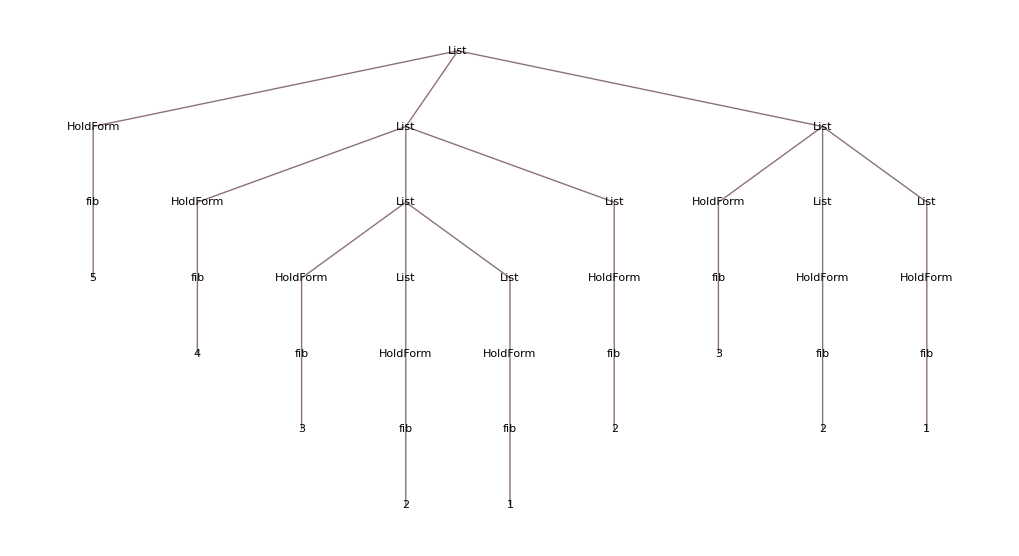

```mathematica
TreeForm@Trace[fib[5],fib[n_Integer]]
```

Compute the first 200 Fibonacci numbers using rule-based programming (NB: modify the code you wrote in the previous exercise so as to use dynamic programming, i.e., saving intermediate results).

Verify that the 200^th Fibonacci number you have computed agrees with that obtained using the built-in function Fibonacci. [1 Mark]

Use ListLogPlot to show the logarithm of the Fibonacci numbers you have just computed. What do you observe? [2 Marks]

Compute (and numerically evaluate) the successive ratios of Fibonacci numbers F_(n+1)/F_n (Hint: RotateLeft is useful here. Note that you can take the ratio of two (nonzero) lists by dividing one list by the other).Determine the limit of this ratio correct to 80 decimal places. [1 Mark]

Use RootApproximant to obtain the exact value of this ratio. [1 Mark]

Solution

Compute the first 200 Fibonacci numbers using rule-based programming (NB: modify the code you wrote in the previous exercise so as to use dynamic programming, i.e., saving intermediate results). [1 Mark]

```mathematica
Clear[fib]
```

```mathematica
fib[1]=1
```

1

```mathematica
fib[2]=1
```

1

```mathematica
fib[n_]:=(fib[n]=fib[n-1]+fib[n-2])
```

```mathematica
fibs=Table[fib[n],{n,200}];
```

Verify that the 200^th Fibonacci number you have computed agrees with that obtained using the built-in function Fibonacci. [1 Mark]

```mathematica
fib[200]==Fibonacci[200]
```

True

Use ListLogPlot to show the logarithm of the Fibonacci numbers you have just computed. What do you observe? [2 Marks]

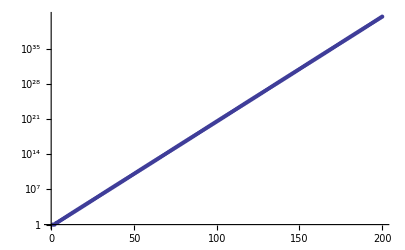

```mathematica
ListLogPlot[fibs]
```

The plot appears to be linear implying exponential growth in the Fibonacci numbers.

Compute (and numerically evaluate) the successive ratios of Fibonacci numbers F_(n+1)/F_n (Hint: RotateLeft is useful here. Note that you can take the ratio of two (nonzero) lists by dividing one list by the other). Determine the limit of this ratio correct to 80 decimal places. [1 Mark]

```mathematica
Most[N[RotateLeft[fibs]/fibs,90]]
```

{1.,2.,1.5,1.66666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,1.6,1.625,1.61538461538461538461538461538461538461538461538461538461538461538461538461538461538461538,1.61904761904761904761904761904761904761904761904761904761904761904761904761904761904761905,1.61764705882352941176470588235294117647058823529411764705882352941176470588235294117647059,1.61818181818181818181818181818181818181818181818181818181818181818181818181818181818181818,1.61797752808988764044943820224719101123595505617977528089887640449438202247191011235955056,1.61805555555555555555555555555555555555555555555555555555555555555555555555555555555555556,1.61802575107296137339055793991416309012875536480686695278969957081545064377682403433476395,1.61803713527851458885941644562334217506631299734748010610079575596816976127320954907161804,1.6180327868852459016393442622950819672131147540983606557377049180327868852459016393442623,1.6180344478216818642350557244174265450861195542046605876393110435663627152988855116514691,1.6180338134001252348152786474639949906073888541014402003757044458359423919849718221665623,1.61803405572755417956656346749226006191950464396284829721362229102167182662538699690402477,1.61803396316670652953838794546759148529060033484812245874192776847644104281272422865343219,1.61803399852180339985218033998521803399852180339985218033998521803399852180339985218033999,1.61803398501735793897314087337840306961447103964918691759546866435227480358121688287959072,1.61803399017559708655637739258088193777878154819039015301225227259894980520580430241093106,1.61803398820532505147084481976480441078968489374323899919740377569180304986565237114841051,1.61803398895790200138026224982746721877156659765355417529330572808833678398895790200138026,1.6180339886704431856047984005331556147950683105631456181272909030323225591469510163278907,1.61803398878024268285650737686687041262675772079114940729696110978392493801125270814626873,1.61803398873830300685273243796393405899662963679499842173324237086214094431263937113706483,1.61803398875432253760883040549257262964466302299165227131848803219523553306839599636261803,1.61803398874820362134379819107829391185639082976650480622446419785737482716844051969064366,1.61803398875054083938272198451997500120186529493774337772222489303398875054083938272198452,1.6180339887496481015309718934328874838535240728264559311697736485056106914739921962104156,1.6180339887499890970472967792907250532408395686746003436610692055167563463218487367953766,1.61803398874985884835007198024841555499693864059754103895558560485822699909038755845380638,1.61803398874990859892542145758806022283099770344388728024945961580511765356739490016197059,1.61803398874988959589659781966119622236443053427999997832557479220999483606819424403126969,1.61803398874989685440771925537991334698605900249371213753031408770536689289040204812317888,1.6180339887498940819031785860452540061877279722749783227515963052456271193709266031777623,1.61803398874989514090567915831514134110502848061263754769377915859911473469120541307524535,1.6180339887498947364027181108378957045590213424769755348584493567702462572091136345000614,1.618033988749894890909100680999418033988749894890909100680999418033988749894890909100681,1.61803398874989483189291401799204893780106154155286049671862521242810150765604191628270204,1.61803398874989485443509143685262693111382156329574887634962189550347847059270028651251966,1.6180339887498948458247458432782610310637042846296087532029851631060262025923068535248585,1.61803398874989484911360520514078058962519361731414313599656877953357332948975415736661494,1.61803398874989484785737271312758779235765109370520129924388174896013375308485568861350524,1.61803398874989484833721082730464662244254918386813942032155961034469208034099422814665489,1.61803398874989484815392897678666292899490820535427460117761727577234864142061384864279059,1.61803398874989484822393641416355517918574857727433789858779983265974293723859075439954432,1.61803398874989484819719595255086212205106635745185384537231876012295828219717843480838633,1.61803398874989484820740990001204904326284254042472288566070913139408284656461170787663185,1.61803398874989484820350851924118133676198756188312004450422917555443701989513585471473336,1.61803398874989484820499871409259753505274587299122093508565152632979656308799355455352988,1.61803398874989484820442951030921664668132147684713072980726254463844043047836552484948295,1.61803398874989484820464692680794311350483570618540642482642118725254750788459174137858879,1.61803398874989484820456388109514460140571731977480170809583445898175296047561667686448294,1.61803398874989484820459560173481367087955823587515933484252347833414307375423832762757418,1.61803398874989484820458348552860497455715387197229320930315527072920960032790057790936567,1.6180339887498948482045881135075619940505260472869290533912682523085601101335992663426854,1.61803398874989484820458634577689963189281388520305126821306703981252779411570311274641457,1.61803398874989484820458702098992969887257819613379903627024699006393718305629207606659259,1.61803398874989484820458676308150186009099742542452169200496388756729608140980819677369323,1.61803398874989484820458686159375530945597542662147292322933270079403030005292425128611805,1.61803398874989484820458682396542280014262219373987716449335001976645611460778980180089184,1.61803398874989484820458683833816687871770389118771037769411438672613573154861340892801085,1.61803398874989484820458683284826715230581203172580608367625927044452265207170306557951017,1.61803398874989484820458683494522225296640591266368569225106224021495209561614544696870279,1.61803398874989484820458683414425667739651612931195115175006705881231401294104236309519069,1.61803398874989484820458683445019830344559159842927516339515792675378917473657057009791121,1.61803398874989484820458683433333900086825497442903766877367994723289710474640465800165032,1.61803398874989484820458683437797528255118937731242614096571082465637512465592222664414228,1.618033988749894848204586834360925740079722792662498219007111376621876604338056083221672,1.61803398874989484820458683436743808581118814372889351269029746950492145959123345835404202,1.61803398874989484820458683436495059108825867517963555359925381759643314419272242052266693,1.61803398874989484820458683436590072952558172976101413718918630517886003122806625437983224,1.61803398874989484820458683436553780893654203456613634551043068881396752812830751496431667,1.61803398874989484820458683436567643226633806556939113695676478690351025255358387413052478,1.61803398874989484820458683436562348286598966775450455429651807056691945489915963516059776,1.61803398874989484820458683436564370773723883019590951083092411587987112892733471191961624,1.61803398874989484820458683436563598252383974068658122388795269545951607040683865460742472,1.61803398874989484820458683436563893329278784677316112818246091128827172781720756873409365,1.61803398874989484820458683436563780619934261802274970224190768420494573933638268231513142,1.6180339887498948482045868343656382367107301981874040757690591496236273680999331990382076,1.61803398874989484820458683436563807227001268644385238112815798045053779018043413778909722,1.61803398874989484820458683436563813508077764150985309152371002255107081367622925072858525,1.61803398874989484820458683436563811108920028805540265497795506542255343072395449206470705,1.6180339887498948482045868343656381202531673933527532542196678947075714048934158415399492,1.61803398874989484820458683436563811675284343091515189304028436398103469738072033783429447,1.61803398874989484820458683436563811808984821293060537733672212687562682124480981544627551,1.61803398874989484820458683436563811757915782932184628562679236891838715359007331205160654,1.61803398874989484820458683436563811777422419813267007646014387989551403216858400880270938,1.61803398874989484820458683436563811769971547530895779567001910492137306401168664546198917,1.61803398874989484820458683436563811772817527496927084720704191886666908989276493917940537,1.61803398874989484820458683436563811771730459881204397338609825200492198040480750097446667,1.61803398874989484820458683436563811772145682762341154331190643864486728298736517867163599,1.61803398874989484820458683436563811771987081734653570735542554558677848472761510177686283,1.61803398874989484820458683436563811772047661936579564529906003812109957692430262390681628,1.618033988749894848204586834365638117720245223584891667424637453576225098593989400419556,1.61803398874989484820458683436563811772033360890834366310427071467652744138824144166336855,1.61803398874989484820458683436563811772029984871889165393979351592049489133579852579526038,1.61803398874989484820458683436563811772031274396379568575359185108829019869887522987627156,1.6180339887498948482045868343656381177203078184185355994766740443409368266620880331687715,1.61803398874989484820458683436563811772030969980941182649362912941520163540937291916173852,1.61803398874989484820458683436563811772030898118204323171968168093976058120430545788325825,1.61803398874989484820458683436563811772030925567327278902456894129181893507222295572469918,1.61803398874989484820458683436563811772030915082695271188385460871108492767353792347870597,1.61803398874989484820458683436563811772030919087468338600111034610122859600167552237522268,1.61803398874989484820458683436563811772030917557781144079005746651153159841594775793166256,1.61803398874989484820458683436563811772030918142069660230596036789047892284499345236582575,1.61803398874989484820458683436563811772030917918891306296930454334333394714358413350689623,1.61803398874989484820458683436563811772030918004137851946336911560582154981876639564952158,1.61803398874989484820458683436563811772030917971576568931783122336550371749462892808057504,1.61803398874989484820458683436563811772030917984013872326038032782396961179185906864478932,1.61803398874989484820458683436563811772030917979263245157827090668888976122430611452109302,1.61803398874989484820458683436563811772030917981077823268205006563566341862973483632796763,1.61803398874989484820458683436563811772030917980384716105282200993042229698100162503104011,1.61803398874989484820458683436563811772030917980649459483672701809937200452177253711494806,1.61803398874989484820458683436563811772030917980548336511424004929776400354819301216015173,1.61803398874989484820458683436563811772030917980586962049779594753363829892816067494063277,1.61803398874989484820458683436563811772030917980572208406961522162762341376183721155398597,1.61803398874989484820458683436563811772030917980577843797060150110979377388083993893344533,1.61803398874989484820458683436563811772030917980575691269582338856929757869015522018171405,1.61803398874989484820458683436563811772030917980576513461917144670861580414320664905744853,1.61803398874989484820458683436563811772030917980576199412390538483115732297473708118197639,1.61803398874989484820458683436563811772030917980576319368635551232421454102709435593265833,1.61803398874989484820458683436563811772030917980576273549427119172250136803849209955608465,1.61803398874989484820458683436563811772030917980576291050807402603458366895194159393512374,1.61803398874989484820458683436563811772030917980576284365874984370004993920019536717458016,1.6180339887498948482045868343656381177203091798057628691929195563915688275419845530771718,1.61803398874989484820458683436563811772030917980576285943973460065154589226836322212994045,1.61803398874989484820458683436563811772030917980576286316511975518009580974743802906904288,1.61803398874989484820458683436563811772030917980576286174214924733446899258383493919896695,1.61803398874989484820458683436563811772030917980576286228567561634279952659556940187009231,1.61803398874989484820458683436563811772030917980576286207806701716343474172396910372679215,1.61803398874989484820458683436563811772030917980576286215736644569319856232703553548556726,1.6180339887498948482045868343656381177203091798057628621270767592832718853894365383525421,1.61803398874989484820458683436563811772030917980576286213864638998328809559916709799284246,1.61803398874989484820458683436563811772030917980576286213422718429316614190757441620496654,1.61803398874989484820458683436563811772030917980576286213591517066351579277262190192829394,1.61803398874989484820458683436563811772030917980576286213527041724258879386907212654618767,1.61803398874989484820458683436563811772030917980576286213551669113502013971467396696917908,1.61803398874989484820458683436563811772030917980576286213542262287865310108141822108231111,1.6180339887498948482045868343656381177203091798057628621354585537553228711355836183199236,1.61803398874989484820458683436563811772030917980576286213544482938168059960634317249395411,1.6180339887498948482045868343656381177203091798057628621354500716259376441398991127342501,1.6180339887498948482045868343656381177203091798057628621354480692668087820684717378393316,1.61803398874989484820458683436563811772030917980576286213544883409993832374919792228379111,1.61803398874989484820458683436563811772030917980576286213544854195967856077844674384533109,1.61803398874989484820458683436563811772030917980576286213544865354732830800997409471625163,1.61803398874989484820458683436563811772030917980576286213544861092463882928614322054195003,1.6180339887498948482045868343656381177203091798057628621354486272050575182261084921939343,1.61803398874989484820458683436563811772030917980576286213544862098649093013004355141228308,1.61803398874989484820458683436563811772030917980576286213544862336177200547827310210525248,1.6180339887498948482045868343656381177203091798057628621354486224544953675296493908079955,1.61803398874989484820458683436563811772030917980576286213544862280104420602729097400679703,1.61803398874989484820458683436563811772030917980576286213544862266867432848298993570764942,1.61803398874989484820458683436563811772030917980576286213544862271923512261825146740629072,1.61803398874989484820458683436563811772030917980576286213544862269992261775676791060951443,1.61803398874989484820458683436563811772030917980576286213544862270729933820595704930120201,1.61803398874989484820458683436563811772030917980576286213544862270448168171987319002291557,1.61803398874989484820458683436563811772030917980576286213544862270555793072893562916608731,1.61803398874989484820458683436563811772030917980576286213544862270514684018783217101485852,1.61803398874989484820458683436563811772030917980576286213544862270530386280208010632537315,1.61803398874989484820458683436563811772030917980576286213544862270524388550043975854505804,1.61803398874989484820458683436563811772030917980576286213544862270526679479111286657548875,1.61803398874989484820458683436563811772030917980576286213544862270525804422073389026451174,1.61803398874989484820458683436563811772030917980576286213544862270526138664119771116701205,1.61803398874989484820458683436563811772030917980576286213544862270526010995018522477048812,1.61803398874989484820458683436563811772030917980576286213544862270526059760275886305755961,1.61803398874989484820458683436563811772030917980576286213544862270526041133605043459286908,1.61803398874989484820458683436563811772030917980576286213544862270526048248360208169986916,1.61803398874989484820458683436563811772030917980576286213544862270526045530765556884355945,1.61803398874989484820458683436563811772030917980576286213544862270526046568794346030548851,1.61803398874989484820458683436563811772030917980576286213544862270526046172302629877601103,1.61803398874989484820458683436563811772030917980576286213544862270526046323748989190251441,1.61803398874989484820458683436563811772030917980576286213544862270526046265901627405248175,1.61803398874989484820458683436563811772030917980576286213544862270526046287997353447607636,1.6180339887498948482045868343656381177203091798057628621354486227052604627955753710553252,1.61803398874989484820458683436563811772030917980576286213544862270526046282781260089398405,1.61803398874989484820458683436563811772030917980576286213544862270526046281549907479875866,1.61803398874989484820458683436563811772030917980576286213544862270526046282020242324577599,1.6180339887498948482045868343656381177203091798057628621354486227052604628184059039999494,1.61803398874989484820458683436563811772030917980576286213544862270526046281909211329041183,1.61803398874989484820458683436563811772030917980576286213544862270526046281883000466485113,1.6180339887498948482045868343656381177203091798057628621354486227052604628189301212510708,1.61803398874989484820458683436563811772030917980576286213544862270526046281889188011797249,1.61803398874989484820458683436563811772030917980576286213544862270526046281890648693104774,1.61803398874989484820458683436563811772030917980576286213544862270526046281890090762492031,1.61803398874989484820458683436563811772030917980576286213544862270526046281890303873022735,1.61803398874989484820458683436563811772030917980576286213544862270526046281890222472043367,1.61803398874989484820458683436563811772030917980576286213544862270526046281890253564450768,1.61803398874989484820458683436563811772030917980576286213544862270526046281890241688207933,1.61803398874989484820458683436563811772030917980576286213544862270526046281890246224529037,1.61803398874989484820458683436563811772030917980576286213544862270526046281890244491808559,1.61803398874989484820458683436563811772030917980576286213544862270526046281890245153648888,1.61803398874989484820458683436563811772030917980576286213544862270526046281890244900848378,1.6180339887498948482045868343656381177203091798057628621354486227052604628189024499740958,1.61803398874989484820458683436563811772030917980576286213544862270526046281890244960526483,1.61803398874989484820458683436563811772030917980576286213544862270526046281890244974614573,1.61803398874989484820458683436563811772030917980576286213544862270526046281890244969233401}

Use RootApproximant to obtain the exact value of this ratio. [1 Mark]

```mathematica
RootApproximant[Last[%]]
```

1/2 (1+√5)

It is interesting to look at the pattern of the digits, base 2:

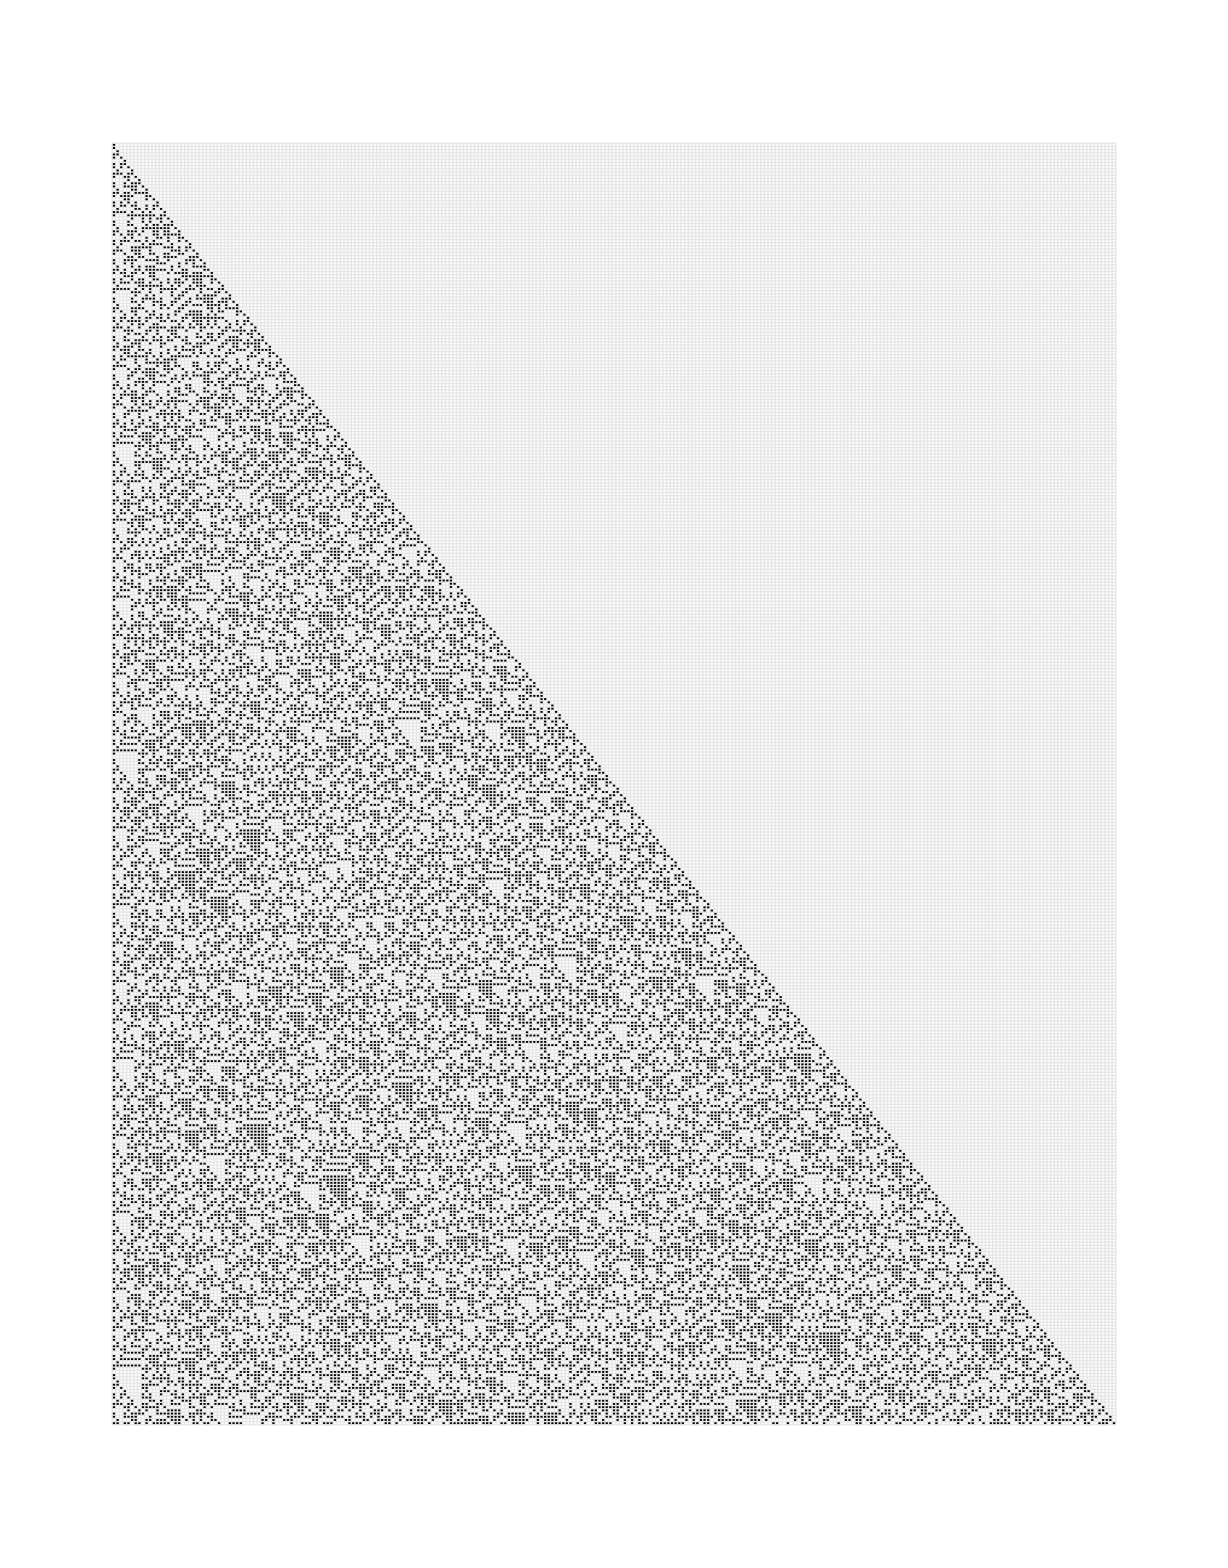

```mathematica
ArrayPlot[Reverse/@IntegerDigits[Fibonacci[Range[400]],2],Mesh->All,MeshStyle->GrayLevel[0.9]]
```

## Functional Programming

Write a function called SumDigits that uses functional programming to compute the total of the digits of an integer n (Hint: use IntegerDigits and Total). Apply SumDigits to 12345678910. [2 Marks]

Write a function called DigitalRoot that applies SumDigits repeatedly to n until the result does not change. (Hint: use FixedPointList). Apply DigitalRoot to 2384729347932847927342389479823. [2 Marks]

Compute the first 1000 Prime numbers. Use Map to apply DigitalRoot to each of these prime numbers and then apply Union to the result. Explain why the single-digit numbers 0, 6, and 9 are missing from this list. Hint: if a number is divisible by 3, what property applies to the sum of its digits? [3 Marks]

Solution

SumDigits uses functional programming (IntegerDigits and Total)  to compute the total of the digits of an integer n:  [1 Mark]

```mathematica
SumDigits[n_Integer]:=Total[IntegerDigits[n]]
```

Apply SumDigits to 12345678910: [1 Mark]

```mathematica
SumDigits[12345678910]
```

46

Use FixedPointList to write a function called DigitalRoot that applies SumDigits repeatedly to n until the result does not change: [1 Mark]

```mathematica
DigitalRoot[n_Integer]:=FixedPoint[SumDigits,n]
```

Apply DigitalRoot to 2384729347932847927342389479823: [1 Mark]

```mathematica
DigitalRoot[2384729347932847927342389479823]
```

{2384729347932847927342389479823,162,9,9}

Compute the first 1000 Prime numbers. Use Map to apply DigitalRoot to each of these prime numbers and then apply Union to the result:  [1 Mark]

```mathematica
Map[DigitalRoot,Prime[Range[1000]]]//Union
```

{1,2,3,4,5,7,8}

The single-digit number 0 is missing from this list because the digit sum must be ≥1. [1 Mark]

The single-digit numbers 6 and 9 are missing because a number is divisible by 3 if and only if the sum of its digits is divisible by 3 and, apart from the number 3, such numbers cannot be prime. [1 Mark]

The logistic map f_μ(x)=μ x (1-x) is an example of a dynamical system. Here is one way of implementing this map.

```mathematica
Subscript[f, μ_][x_]:=μ x (1-x)
```

Iterate f_2 twenty times starting at x=0.3 using NestList. To what value does it converge? [2 Marks]

Compute the fixed point (using FixedPoint or FixedPointList) of this map for μ=2.5 starting from a randomly chosen value x such that 0<x<1 (using RandomReal). [1 Mark]

Compute exactly the fixed points of f_μ(x) (Hint: Solve the equation f_μ(x)==x for x). [1 Mark]

Compute exactly the fixed points of the first iterate of the map, f_μ(f_μ(x)). Determine these four fixed points for μ=2,3,7/2,4.  [2 Marks]

Use ListPlot and Manipulate to display the behaviour of n iterates of f_μ for 2<μ<4 for starting values x_0 in the range 0<x_0<1. Allow n to take on the values 10,50,100,200,500. Relate the behaviour you see to the results you have obtained earlier in this question. Note: it is useful to restrict the PlotRange to {0,1}. [4 Marks]

Solution

Iterate f_2 twenty times starting at x=0.3 using NestList. [1 Mark]

```mathematica
Subscript[f, μ_][x_]:=μ x (1-x)
```

```mathematica
NestList[Subscript[f, 2],0.3,20]
```

{0.3,0.42,0.4872,0.499672,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

To what value does it converge? [1 Mark]

```mathematica
FixedPoint[Subscript[f, 2],0.3]
```

0.5

Compute the fixed point (using FixedPoint or FixedPointList) of this map for μ=2.5 starting from a randomly chosen value x such that 0<x<1 (using RandomReal). [1 Mark]

```mathematica
FixedPoint[Subscript[f, 2.5],RandomReal[]]
```

0.6

Compute exactly the fixed points of f_μ(x) (Hint: Solve the equation f_μ(x)==x for x). [1 Mark]

```mathematica
Solve[Subscript[f, μ](x)==x,x]//Expand
```

{{x→0},{x→1-1/μ}}

Compute exactly the fixed points of the first iterate of the map, f_μ(f_μ(x)). Determine these four fixed points for μ=2,3,7/2,4.  [2 Marks]

```mathematica
Solve[Subscript[f, μ](Subscript[f, μ](x))==x,x]//FullSimplify//Expand
```

{{x→0},{x→1-1/μ},{x→-(√((μ-3) (μ+1)))/(2 μ)+1/(2 μ)+1/2},{x→(√((μ-3) (μ+1)))/(2 μ)+1/(2 μ)+1/2}}

```mathematica
Table[{μ,%},{μ,{2,3,7/2,4}}]
```

(2 | {{x→0},{x→1/2},{x→3/4-(ⅈ √3)/4},{x→3/4+(ⅈ √3)/4}}
3 | {{x→0},{x→2/3},{x→2/3},{x→2/3}}
7/2 | {{x→0},{x→5/7},{x→3/7},{x→6/7}}
4 | {{x→0},{x→3/4},{x→5/8-(√5)/8},{x→5/8+(√5)/8}})

Use ListPlot and Manipulate to display the behaviour of n iterates of f_μ for 2<μ<4 for starting values x_0 in the range 0<x_0<1. Allow n to take on the values 10,50,100,200,500. Relate the behaviour you see to the results you have obtained earlier in this question. Note: it is useful to restrict the PlotRange to {0,1}. [4 Marks]

```mathematica
Manipulate[ListPlot[NestList[Subscript[f, μ],x0,n],Filling->Axis,PlotRange->{0,1},Mesh->All],{μ,2,4},{{x0,0.6},0,1},{{n,50},{10,50,100,200,500}},SaveDefinitions->True]
```

When 2≤μ≤3 there is a single fixed point (apart from x==0) at x==1-μ^-1. For 3<μ≲3.45 the value cycles between two values for starting values 0<x_0<1. For 3.45≲μ≤4 the behaviour becomes more complicated.

## Pattern-matching

Use ReplaceList to construct a list of all three-element subsets of the list {a,b,c,d,e}. [2 Marks]

Use ReplaceList to find all single elements of {a,b,a,b,a,e,f,a,c,a,c} that are flanked by the same element. [2 Marks]

Use pattern-matching to find three numbers in {6,44,30,15,24,12,33,23,18,8} whose square sums to 1269. Is the solution unique? [2 Marks]

Solution

Use ReplaceList to construct a list of all three-element subsets of the list {a,b,c,d,e}: [2 Marks]

```mathematica
ReplaceList[{a,b,c,d,e},{___,x_,___,y_,___,z_,___}->{x,y,z}]
```

(a | b | c
a | b | d
a | b | e
a | c | d
a | c | e
a | d | e
b | c | d
b | c | e
b | d | e
c | d | e)

Use ReplaceList to find all single elements of {a,b,a,b,a,e,f,a,c,a,c} that are flanked by the same element: [2 Marks]

```mathematica
ReplaceList[{a,b,a,b,a,e,f,a,c,a,c},{___,x_,y_,x_,___}->{x,{y}}]
```

(a | {b}
b | {a}
a | {b}
a | {c}
c | {a})

Use pattern-matching to find three numbers in {6,44,30,15,24,12,33,23,18,8} whose square sums to 1269. [1 Mark]

```mathematica
{6,44,30,15,24,12,33,23,18,8}/.{___,x_,___,y_,___,z_,___}:>{x,y,z}/;x^2+y^2+z^2==1269
```

{6,12,33}

The solution is not unique: [1 Mark]

```mathematica
ReplaceList[{6,44,30,15,24,12,33,23,18,8},{___,x_,___,y_,___,z_,___}:>{x,y,z}/;x^2+y^2+z^2==1269]
```

(6 | 12 | 33
30 | 15 | 12)